## RNN

```mathematica
ImportDataset["10_40.mx"]
```

```mathematica
lengths = x;
```

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,#[[2]]==True&];
Length[NoHalt]
Length[Halt]
```

862

```mathematica
HaltTrain = RandomSample[Halt,Length[NoHalt]];
trainhalt=Partition[HaltTrain,Length[HaltTrain]/2][[1]];
testhalt = Partition[HaltTrain,Length[HaltTrain]/2][[2]];
trainnohalt=Partition[NoHalt,Length[NoHalt]/2][[1]];
testnohalt = Partition[NoHalt,Length[NoHalt]/2][[2]];
TrainingData = Join[trainhalt,trainnohalt];
TrainingData2 = ConvertSKTableToString[TrainingData];
TestingData = Join[testhalt,testnohalt];
TestingData2 = ConvertSKTableToString[TestingData];
Length[TrainingData2]
```

862

```mathematica
net=NetChain[{EmbeddingLayer[500],DropoutLayer[0.3],LongShortTermMemoryLayer[500],SequenceLastLayer[],LinearLayer[2],SoftmaxLayer[]},"Input"->NetEncoder[{"Characters"}],"Output"->NetDecoder[{"Class",{True,False}}]]
```

NetChain[<>]

```mathematica
trained=NetTrain[net,TrainingData2,ValidationSet->TestingData2]
```

$Aborted[]

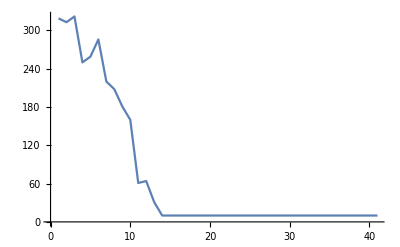
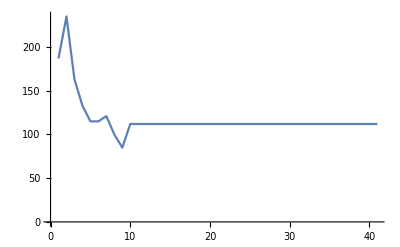
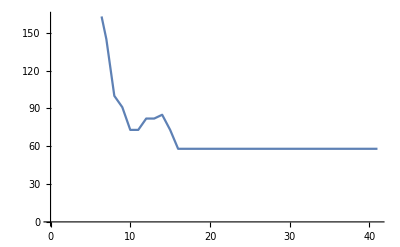
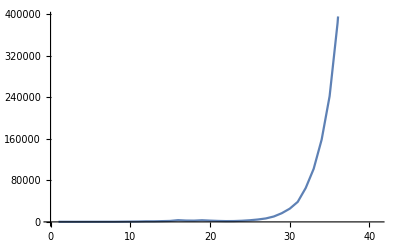
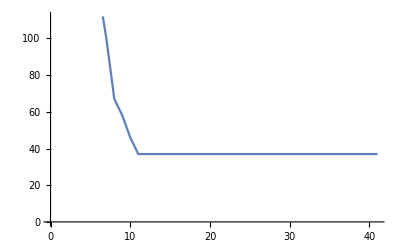
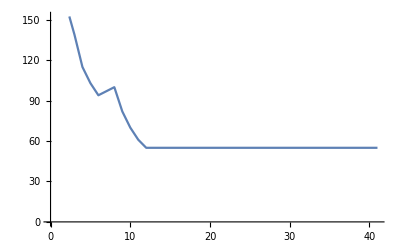
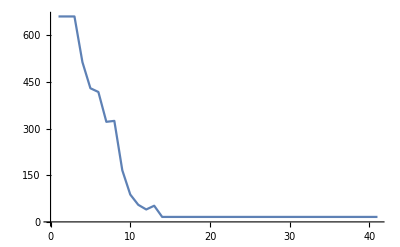
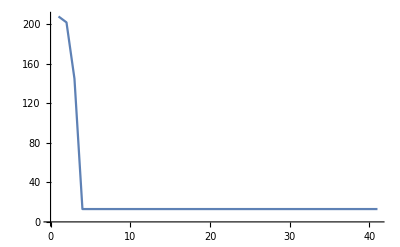
{{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False}}

```mathematica
Table[TestClassifier[trained,TestingData2],20]
```

## Markov

```mathematica
Markov=Classify[TrainingData2]
```

ClassifierFunction[…]

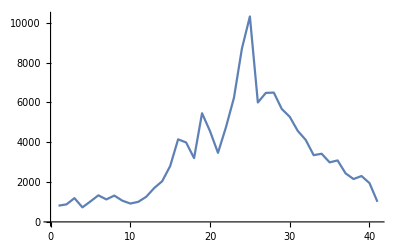
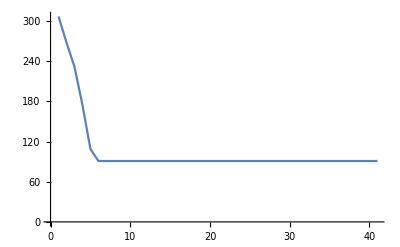
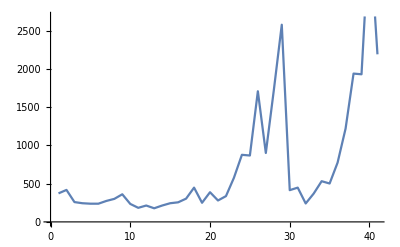
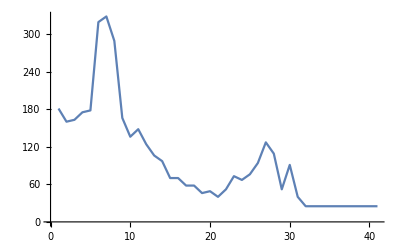
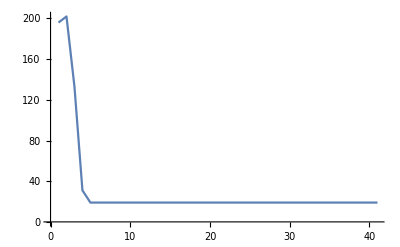
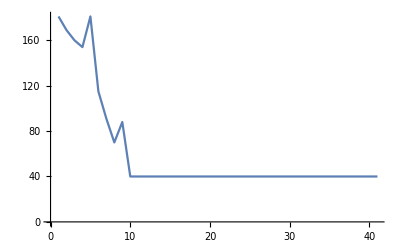
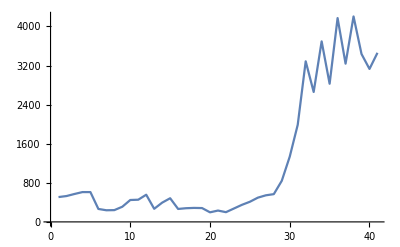
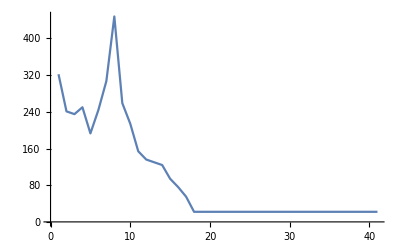
{{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False}}

```mathematica
Table[TestClassifier[Markov,TestingData2],20]
```